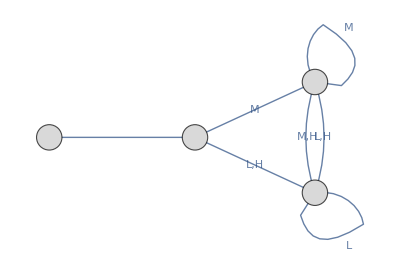

x0.png

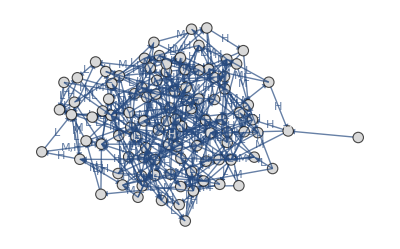

x1.png

```mathematica
SetDirectory[NotebookDirectory[]];
   VertexCircle[{xc_, yc_}, name_, {w_, h_}] := Disk[{xc, yc}, .1];
x0Graph =
   Graph[{-1 -> 2 ,
Labeled[0 -> 1, "L,H"], Labeled[0 -> 0, "M"], Labeled[1 -> 1, "L"], Labeled[1 -> 0, "M,H"], Labeled[2 -> 1, "L,H"], Labeled[2 -> 0, "M"]     },
   EdgeShapeFunction -> 
    GraphElementData["EdgeShapeFunction", "FilledArrow"],
   VertexStyle -> LightGray,
   VertexShapeFunction -> VertexCircle,
   VertexLabels -> {0 -> Placed["H", Center], 1 -> Placed["H", Center], 2 -> Placed["L", Center]}
   ];
S = Show[x0Graph]
Export["x0.png",S]
 
SetDirectory[NotebookDirectory[]];
   VertexCircle[{xc_, yc_}, name_, {w_, h_}] := Disk[{xc, yc}, .1];
x1Graph =
   Graph[{-1 -> 90 ,
Labeled[0 -> 39, "L"], Labeled[0 -> 18, "M"], Labeled[0 -> 72, "H"], Labeled[1 -> 57, "L"], Labeled[1 -> 52, "M"], Labeled[1 -> 45, "H"], Labeled[2 -> 67, "L"], Labeled[2 -> 53, "M"], Labeled[2 -> 98, "H"], Labeled[3 -> 32, "L"], Labeled[3 -> 96, "M"], Labeled[3 -> 95, "H"], Labeled[4 -> 69, "L"], Labeled[4 -> 57, "M"], Labeled[4 -> 42, "H"], Labeled[5 -> 87, "L"], Labeled[5 -> 4, "M"], Labeled[5 -> 69, "H"], Labeled[6 -> 51, "L"], Labeled[6 -> 18, "M"], Labeled[6 -> 4, "H"], Labeled[7 -> 25, "L"], Labeled[7 -> 77, "M"], Labeled[7 -> 87, "H"], Labeled[8 -> 16, "L"], Labeled[8 -> 77, "M"], Labeled[8 -> 0, "H"], Labeled[9 -> 94, "L"], Labeled[9 -> 37, "M"], Labeled[9 -> 28, "H"], Labeled[10 -> 3, "L"], Labeled[10 -> 87, "M"], Labeled[10 -> 63, "H"], Labeled[11 -> 62, "L"], Labeled[11 -> 6, "M"], Labeled[11 -> 0, "H"], Labeled[12 -> 83, "L,H"], Labeled[12 -> 81, "M"], Labeled[13 -> 56, "L"], Labeled[13 -> 73, "M"], Labeled[13 -> 37, "H"], Labeled[14 -> 36, "L"], Labeled[14 -> 7, "M"], Labeled[14 -> 19, "H"], Labeled[15 -> 10, "L"], Labeled[15 -> 34, "M"], Labeled[15 -> 43, "H"], Labeled[16 -> 21, "L"], Labeled[16 -> 45, "M"], Labeled[16 -> 64, "H"], Labeled[17 -> 94, "L"], Labeled[17 -> 62, "M"], Labeled[17 -> 13, "H"], Labeled[18 -> 96, "L"], Labeled[18 -> 44, "M"], Labeled[18 -> 94, "H"], Labeled[19 -> 75, "L"], Labeled[19 -> 8, "M"], Labeled[19 -> 49, "H"], Labeled[20 -> 88, "L"], Labeled[20 -> 74, "M"], Labeled[20 -> 82, "H"], Labeled[21 -> 52, "L"], Labeled[21 -> 14, "M"], Labeled[21 -> 99, "H"], Labeled[22 -> 18, "L"], Labeled[22 -> 68, "M"], Labeled[22 -> 93, "H"], Labeled[23 -> 25, "L"], Labeled[23 -> 97, "M"], Labeled[23 -> 54, "H"], Labeled[24 -> 22, "L"], Labeled[24 -> 70, "M"], Labeled[24 -> 83, "H"], Labeled[25 -> 99, "L"], Labeled[25 -> 55, "M"], Labeled[25 -> 39, "H"], Labeled[26 -> 14, "L"], Labeled[26 -> 19, "M"], Labeled[26 -> 25, "H"], Labeled[27 -> 76, "L"], Labeled[27 -> 60, "M"], Labeled[27 -> 54, "H"], Labeled[28 -> 86, "L"], Labeled[28 -> 69, "M"], Labeled[28 -> 56, "H"], Labeled[29 -> 83, "L"], Labeled[29 -> 2, "M"], Labeled[29 -> 63, "H"], Labeled[30 -> 76, "L"], Labeled[30 -> 79, "M"], Labeled[30 -> 27, "H"], Labeled[31 -> 77, "L"], Labeled[31 -> 86, "M"], Labeled[31 -> 48, "H"], Labeled[32 -> 63, "L"], Labeled[32 -> 18, "M"], Labeled[32 -> 37, "H"], Labeled[33 -> 8, "L"], Labeled[33 -> 3, "M"], Labeled[33 -> 30, "H"], Labeled[34 -> 30, "L"], Labeled[34 -> 48, "M"], Labeled[34 -> 39, "H"], Labeled[35 -> 72, "L"], Labeled[35 -> 68, "M"], Labeled[35 -> 76, "H"], Labeled[36 -> 8, "L"], Labeled[36 -> 69, "M"], Labeled[36 -> 38, "H"], Labeled[37 -> 48, "L"], Labeled[37 -> 8, "M"], Labeled[37 -> 52, "H"], Labeled[38 -> 29, "L"], Labeled[38 -> 37, "M"], Labeled[38 -> 33, "H"], Labeled[39 -> 89, "L"], Labeled[39 -> 31, "M"], Labeled[39 -> 41, "H"], Labeled[40 -> 78, "L"], Labeled[40 -> 86, "M"], Labeled[40 -> 59, "H"], Labeled[41 -> 62, "L"], Labeled[41 -> 24, "M"], Labeled[41 -> 64, "H"], Labeled[42 -> 97, "L"], Labeled[42 -> 50, "M"], Labeled[42 -> 16, "H"], Labeled[43 -> 85, "L"], Labeled[43 -> 52, "M"], Labeled[43 -> 18, "H"], Labeled[44 -> 46, "L"], Labeled[44 -> 56, "M"], Labeled[44 -> 18, "H"], Labeled[45 -> 51, "L"], Labeled[45 -> 15, "M"], Labeled[45 -> 73, "H"], Labeled[46 -> 41, "L"], Labeled[46 -> 3, "M"], Labeled[46 -> 19, "H"], Labeled[47 -> 63, "L"], Labeled[47 -> 93, "M"], Labeled[47 -> 3, "H"], Labeled[48 -> 69, "L"], Labeled[48 -> 60, "M"], Labeled[48 -> 92, "H"], Labeled[49 -> 71, "L"], Labeled[49 -> 65, "M"], Labeled[49 -> 35, "H"], Labeled[50 -> 97, "L"], Labeled[50 -> 21, "M"], Labeled[50 -> 85, "H"], Labeled[51 -> 61, "L"], Labeled[51 -> 27, "M"], Labeled[51 -> 36, "H"], Labeled[52 -> 20, "L"], Labeled[52 -> 82, "M"], Labeled[52 -> 23, "H"], Labeled[53 -> 0, "L"], Labeled[53 -> 31, "M"], Labeled[53 -> 74, "H"], Labeled[54 -> 38, "L"], Labeled[54 -> 73, "M"], Labeled[54 -> 36, "H"], Labeled[55 -> 60, "L"], Labeled[55 -> 69, "M"], Labeled[55 -> 90, "H"], Labeled[56 -> 75, "L"], Labeled[56 -> 97, "M"], Labeled[56 -> 91, "H"], Labeled[57 -> 14, "L"], Labeled[57 -> 59, "M"], Labeled[57 -> 56, "H"], Labeled[58 -> 94, "L"], Labeled[58 -> 53, "M"], Labeled[58 -> 73, "H"], Labeled[59 -> 19, "L"], Labeled[59 -> 68, "M"], Labeled[59 -> 62, "H"], Labeled[60 -> 1, "L"], Labeled[60 -> 40, "M"], Labeled[60 -> 61, "H"], Labeled[61 -> 46, "L"], Labeled[61 -> 33, "M"], Labeled[61 -> 91, "H"], Labeled[62 -> 30, "L"], Labeled[62 -> 68, "M"], Labeled[62 -> 34, "H"], Labeled[63 -> 18, "L"], Labeled[63 -> 67, "M"], Labeled[63 -> 10, "H"], Labeled[64 -> 18, "L"], Labeled[64 -> 9, "M"], Labeled[64 -> 68, "H"], Labeled[65 -> 35, "L"], Labeled[65 -> 45, "M"], Labeled[65 -> 77, "H"], Labeled[66 -> 91, "L"], Labeled[66 -> 3, "M"], Labeled[66 -> 39, "H"], Labeled[67 -> 3, "L"], Labeled[67 -> 89, "M"], Labeled[67 -> 15, "H"], Labeled[68 -> 19, "L"], Labeled[68 -> 30, "M"], Labeled[68 -> 8, "H"], Labeled[69 -> 27, "L"], Labeled[69 -> 68, "M"], Labeled[69 -> 38, "H"], Labeled[70 -> 26, "L"], Labeled[70 -> 82, "M"], Labeled[70 -> 14, "H"], Labeled[71 -> 35, "L"], Labeled[71 -> 3, "M"], Labeled[71 -> 44, "H"], Labeled[72 -> 64, "L"], Labeled[72 -> 41, "M"], Labeled[72 -> 44, "H"], Labeled[73 -> 51, "L"], Labeled[73 -> 62, "M"], Labeled[73 -> 6, "H"], Labeled[74 -> 61, "L"], Labeled[74 -> 43, "M"], Labeled[74 -> 24, "H"], Labeled[75 -> 7, "L"], Labeled[75 -> 41, "M"], Labeled[75 -> 58, "H"], Labeled[76 -> 58, "L"], Labeled[76 -> 83, "M"], Labeled[76 -> 76, "H"], Labeled[77 -> 8, "L"], Labeled[77 -> 20, "M"], Labeled[77 -> 95, "H"], Labeled[78 -> 62, "L"], Labeled[78 -> 25, "M"], Labeled[78 -> 61, "H"], Labeled[79 -> 0, "L"], Labeled[79 -> 31, "M"], Labeled[79 -> 2, "H"], Labeled[80 -> 86, "L"], Labeled[80 -> 53, "M"], Labeled[80 -> 99, "H"], Labeled[81 -> 82, "L"], Labeled[81 -> 67, "M"], Labeled[81 -> 93, "H"], Labeled[82 -> 16, "L"], Labeled[82 -> 37, "M"], Labeled[82 -> 83, "H"], Labeled[83 -> 20, "L"], Labeled[83 -> 7, "M"], Labeled[83 -> 81, "H"], Labeled[84 -> 26, "L"], Labeled[84 -> 44, "M"], Labeled[84 -> 97, "H"], Labeled[85 -> 93, "L"], Labeled[85 -> 40, "M"], Labeled[85 -> 73, "H"], Labeled[86 -> 51, "L"], Labeled[86 -> 7, "M"], Labeled[86 -> 27, "H"], Labeled[87 -> 36, "L"], Labeled[87 -> 65, "M"], Labeled[87 -> 62, "H"], Labeled[88 -> 34, "L"], Labeled[88 -> 67, "M"], Labeled[88 -> 73, "H"], Labeled[89 -> 50, "L"], Labeled[89 -> 71, "M"], Labeled[89 -> 95, "H"], Labeled[90 -> 62, "L"], Labeled[90 -> 19, "M"], Labeled[90 -> 59, "H"], Labeled[91 -> 54, "L"], Labeled[91 -> 60, "M"], Labeled[91 -> 25, "H"], Labeled[92 -> 28, "L"], Labeled[92 -> 70, "M"], Labeled[92 -> 62, "H"], Labeled[93 -> 5, "L"], Labeled[93 -> 14, "M"], Labeled[93 -> 57, "H"], Labeled[94 -> 12, "L"], Labeled[94 -> 44, "M"], Labeled[94 -> 78, "H"], Labeled[95 -> 5, "L"], Labeled[95 -> 83, "M"], Labeled[95 -> 85, "H"], Labeled[96 -> 86, "L,M"], Labeled[96 -> 18, "H"], Labeled[97 -> 92, "L,H"], Labeled[97 -> 31, "M"], Labeled[98 -> 67, "L"], Labeled[98 -> 83, "M,H"], Labeled[99 -> 25, "L"], Labeled[99 -> 76, "M"], Labeled[99 -> 2, "H"]     },
   EdgeShapeFunction -> 
    GraphElementData["EdgeShapeFunction", "FilledArrow"],
   VertexStyle -> LightGray,
   VertexShapeFunction -> VertexCircle,
   VertexLabels -> {0 -> Placed["L", Center], 1 -> Placed["M", Center], 2 -> Placed["M", Center], 3 -> Placed["L", Center], 4 -> Placed["M", Center], 5 -> Placed["H", Center], 6 -> Placed["L", Center], 7 -> Placed["H", Center], 8 -> Placed["L", Center], 9 -> Placed["H", Center], 10 -> Placed["H", Center], 11 -> Placed["M", Center], 12 -> Placed["L", Center], 13 -> Placed["L", Center], 14 -> Placed["H", Center], 15 -> Placed["H", Center], 16 -> Placed["M", Center], 17 -> Placed["L", Center], 18 -> Placed["L", Center], 19 -> Placed["H", Center], 20 -> Placed["M", Center], 21 -> Placed["M", Center], 22 -> Placed["M", Center], 23 -> Placed["L", Center], 24 -> Placed["L", Center], 25 -> Placed["H", Center], 26 -> Placed["L", Center], 27 -> Placed["M", Center], 28 -> Placed["M", Center], 29 -> Placed["L", Center], 30 -> Placed["H", Center], 31 -> Placed["M", Center], 32 -> Placed["M", Center], 33 -> Placed["L", Center], 34 -> Placed["H", Center], 35 -> Placed["L", Center], 36 -> Placed["L", Center], 37 -> Placed["M", Center], 38 -> Placed["L", Center], 39 -> Placed["H", Center], 40 -> Placed["H", Center], 41 -> Placed["L", Center], 42 -> Placed["M", Center], 43 -> Placed["H", Center], 44 -> Placed["H", Center], 45 -> Placed["M", Center], 46 -> Placed["L", Center], 47 -> Placed["M", Center], 48 -> Placed["L", Center], 49 -> Placed["L", Center], 50 -> Placed["H", Center], 51 -> Placed["L", Center], 52 -> Placed["M", Center], 53 -> Placed["L", Center], 54 -> Placed["L", Center], 55 -> Placed["H", Center], 56 -> Placed["H", Center], 57 -> Placed["L", Center], 58 -> Placed["M", Center], 59 -> Placed["M", Center], 60 -> Placed["H", Center], 61 -> Placed["M", Center], 62 -> Placed["H", Center], 63 -> Placed["H", Center], 64 -> Placed["H", Center], 65 -> Placed["L", Center], 66 -> Placed["H", Center], 67 -> Placed["H", Center], 68 -> Placed["M", Center], 69 -> Placed["H", Center], 70 -> Placed["L", Center], 71 -> Placed["M", Center], 72 -> Placed["L", Center], 73 -> Placed["M", Center], 74 -> Placed["M", Center], 75 -> Placed["H", Center], 76 -> Placed["M", Center], 77 -> Placed["H", Center], 78 -> Placed["L", Center], 79 -> Placed["H", Center], 80 -> Placed["L", Center], 81 -> Placed["H", Center], 82 -> Placed["L", Center], 83 -> Placed["M", Center], 84 -> Placed["L", Center], 85 -> Placed["H", Center], 86 -> Placed["L", Center], 87 -> Placed["M", Center], 88 -> Placed["L", Center], 89 -> Placed["H", Center], 90 -> Placed["M", Center], 91 -> Placed["M", Center], 92 -> Placed["H", Center], 93 -> Placed["H", Center], 94 -> Placed["L", Center], 95 -> Placed["M", Center], 96 -> Placed["L", Center], 97 -> Placed["L", Center], 98 -> Placed["L", Center], 99 -> Placed["H", Center]}
   ];
S = Show[x1Graph]
Export["x1.png",S]
```